#### gr. 1

Zad. 1

-16 x+20 x^2-8 x^3+x^4

-16+40 x-24 x^2+4 x^3

{{x→2},{x→2-√2},{x→2+√2}}

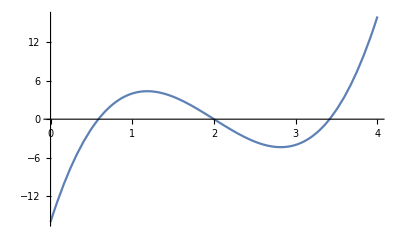

```mathematica
(x-2)((x-2)^2-2)//Expand;
4Integrate[%,x]//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,0,4}]
```

Zad. 2

```mathematica
(* (a) *)
```

```mathematica
L=(x-2)^2(x^2+2)//Expand;
M=(x-2)^2(x-1)(x+2)//Expand;
L/M
Limit[L/M,x->2]
(* (b)  calka od 0 do 2 *)
f[x_]:=4x-x^2;
a1=f[0];
b1=f[1/2];
c1=f[1];
ml=f[0]/2+f[1/2]/2
mr=f[1/2]/2+f[1]/2
```

(8-8 x+6 x^2-4 x^3+x^4)/(-8+12 x-2 x^2-3 x^3+x^4)

3/2

7/8

19/8

Zad. 3

```mathematica
Integrate[4 x^3-2/x^3+1/Sin[x]^2,x]
Integrate[x/((2-4 x^2)^3),x]
Integrate[x Cos[5x],x]
```

1/x^2+x^4-Cot[x]

1/(16 (2-4 x^2)^2)

1/25 Cos[5 x]+1/5 x Sin[5 x]

#### gr. 2

Zad. 1

8-6 x^2+x^4

40 x-10 x^3+x^5

40-30 x^2+5 x^4

{{x→-2},{x→2},{x→-√2},{x→√2}}

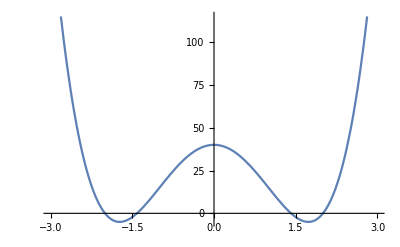

```mathematica
(x^2-2)(x^2-4)//Expand
5Integrate[%,x]//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-3,3}]
```

Zad. 2

```mathematica
(* (a) *)
```

```mathematica
L=x Cos[4x];
M=Exp[10x]-1;
Limit[L/M,x->0]
(* (b) *)
f[x_]:=1/x;
a1=f[1];
b1=f[3/2];
c1=f[2];
mL=(f[1]+f[3/2])/2
mR=(f[3/2]+f[2])/2
```

1/10

5/6

7/12

Zad. 3

```mathematica
Integrate[10/(x^2+1)-3/x^6+2/((x^2)^(1/3)),x]
Integrate[Cos[x]/Sqrt[2+3Sin[x]],x]
Integrate[√x Log[x],x]
```

3/(5 x^5)+(6 (x^2)^(2/3))/x+10 ArcTan[x]

2/3 √(2+3 Sin[x])

2/9 x^(3/2) (-2+3 Log[x])